```mathematica
mis=Delete[ToExpression[Import["~/impedance_exp/misfit_5.csv"]],1]
```

```mathematica
abc=Transpose[Join[{Transpose[mis][[2]]},{Transpose[mis][[3]]},{Log[Transpose[mis][[4]]]}]]
```

{{0.1,0.5,-5.90281},{0.1,1.5,-6.13178},{0.1,2.5,-6.40301},{0.1,3.5,-6.75509},{0.1,4.5,-7.27756},{0.1,5.5,-7.19348},{0.1,6.5,-6.75131},{0.1,7.5,-6.43956},{0.1,8.5,-6.20251},{0.1,9.5,-6.01241},{0.1,10.5,-5.85438},{0.1,11.5,-5.71939},{0.1,12.5,-5.60189},{0.1,13.5,-5.49799},{0.1,14.5,-5.40496},{0.1,15.5,-5.3208},{0.1,16.5,-5.24404},{0.1,17.5,-5.17353},{0.1,18.5,-5.10835},{0.1,19.5,-5.04779},{0.6,0.5,-6.05651},{0.6,1.5,-6.33207},{0.6,2.5,-6.67768},{0.6,3.5,-7.17622},{0.6,4.5,-7.84166},{0.6,5.5,-7.13101},{0.6,6.5,-6.69876},{0.6,7.5,-6.39691},{0.6,8.5,-6.16698},{0.6,9.5,-5.98207},{0.6,10.5,-5.82799},{0.6,11.5,-5.6961},{0.6,12.5,-5.58103},{0.6,13.5,-5.47912},{0.6,14.5,-5.38775},{0.6,15.5,-5.30501},{0.6,16.5,-5.22946},{0.6,17.5,-5.16},{0.6,18.5,-5.09575},{0.6,19.5,-5.03601},{1.1,0.5,-6.21494},{1.1,1.5,-6.54794},{1.1,2.5,-7.00098},{1.1,3.5,-7.78757},{1.1,4.5,-7.63302},{1.1,5.5,-6.99076},{1.1,6.5,-6.59853},{1.1,7.5,-6.31929},{1.1,8.5,-6.10369},{1.1,9.5,-5.92871},{1.1,10.5,-5.78184},{1.1,11.5,-5.65546},{1.1,12.5,-5.54476},{1.1,13.5,-5.44637},{1.1,14.5,-5.35791},{1.1,15.5,-5.27761},{1.1,16.5,-5.20415},{1.1,17.5,-5.13649},{1.1,18.5,-5.07379},{1.1,19.5,-5.01541},{1.6,0.5,-6.37527},{1.6,1.5,-6.77807},{1.6,2.5,-7.39388},{1.6,3.5,-8.37917},{1.6,4.5,-7.31976},{1.6,5.5,-6.80033},{1.6,6.5,-6.46211},{1.6,7.5,-6.21298},{1.6,8.5,-6.01651},{1.6,9.5,-5.85484},{1.6,10.5,-5.71773},{1.6,11.5,-5.59887},{1.6,12.5,-5.49409},{1.6,13.5,-5.4005},{1.6,14.5,-5.31601},{1.6,15.5,-5.23905},{1.6,16.5,-5.16843},{1.6,17.5,-5.10323},{1.6,18.5,-5.04269},{1.6,19.5,-4.98619},{2.1,0.5,-6.5417},{2.1,1.5,-7.03044},{2.1,2.5,-7.92375},{2.1,3.5,-7.70489},{2.1,4.5,-6.9981},{2.1,5.5,-6.59041},{2.1,6.5,-6.30617},{2.1,7.5,-6.08887},{2.1,8.5,-5.91351},{2.1,9.5,-5.76679},{2.1,10.5,-5.64084},{2.1,11.5,-5.53064},{2.1,12.5,-5.43277},{2.1,13.5,-5.34483},{2.1,14.5,-5.26503},{2.1,15.5,-5.19203},{2.1,16.5,-5.12479},{2.1,17.5,-5.06251},{2.1,18.5,-5.00454},{2.1,19.5,-4.9503},{2.6,0.5,-6.71662},{2.6,1.5,-7.30929},{2.6,2.5,-8.14272},{2.6,3.5,-7.14734},{2.6,4.5,-6.67286},{2.6,5.5,-6.36073},{2.6,6.5,-6.1287},{2.6,7.5,-5.94442},{2.6,8.5,-5.79183},{2.6,9.5,-5.66179},{2.6,10.5,-5.5486},{2.6,11.5,-5.44847},{2.6,12.5,-5.35877},{2.6,13.5,-5.27758},{2.6,14.5,-5.20346},{2.6,15.5,-5.1353},{2.6,16.5,-5.07225},{2.6,17.5,-5.01361},{2.6,18.5,-4.95882},{2.6,19.5,-4.90735},{3.1,0.5,-6.90093},{3.1,1.5,-7.60099},{3.1,2.5,-7.30201},{3.1,3.5,-6.75056},{3.1,4.5,-6.40823},{3.1,5.5,-6.16051},{3.1,6.5,-5.9668},{3.1,7.5,-5.80802},{3.1,8.5,-5.67366},{3.1,9.5,-5.55732},{3.1,10.5,-5.45482},{3.1,11.5,-5.36328},{3.1,12.5,-5.28064},{3.1,13.5,-5.20534},{3.1,14.5,-5.13623},{3.1,15.5,-5.07239},{3.1,16.5,-5.01309},{3.1,17.5,-4.95775},{3.1,18.5,-4.90588},{3.1,19.5,-4.8571},{3.6,0.5,-7.09222},{3.6,1.5,-7.5319},{3.6,2.5,-6.85263},{3.6,3.5,-6.46795},{3.6,4.5,-6.19977},{3.6,5.5,-5.99429},{3.6,6.5,-5.82798},{3.6,7.5,-5.68846},{3.6,8.5,-5.5684},{3.6,9.5,-5.46313},{3.6,10.5,-5.36946},{3.6,11.5,-5.28513},{3.6,12.5,-5.20849},{3.6,13.5,-5.13829},{3.6,14.5,-5.07354},{3.6,15.5,-5.01349},{3.6,16.5,-4.95751},{3.6,17.5,-4.90511},{3.6,18.5,-4.85586},{3.6,19.5,-4.80942},{4.1,0.5,-7.27677},{4.1,1.5,-6.99347},{4.1,2.5,-6.5443},{4.1,3.5,-6.24836},{4.1,4.5,-6.0278},{4.1,5.5,-5.85219},{4.1,6.5,-5.70646},{4.1,7.5,-5.58201},{4.1,8.5,-5.4735},{4.1,9.5,-5.37736},{4.1,10.5,-5.2911},{4.1,11.5,-5.21292},{4.1,12.5,-5.14147},{4.1,13.5,-5.0757},{4.1,14.5,-5.01479},{4.1,15.5,-4.9581},{4.1,16.5,-4.90509},{4.1,17.5,-4.85532},{4.1,18.5,-4.80844},{4.1,19.5,-4.76413},{4.6,0.5,-7.21293},{4.6,1.5,-6.64597},{4.6,2.5,-6.30942},{4.6,3.5,-6.06879},{4.6,4.5,-5.88145},{4.6,5.5,-5.72812},{4.6,6.5,-5.59842},{4.6,7.5,-5.48609},{4.6,8.5,-5.38708},{4.6,9.5,-5.29861},{4.6,10.5,-5.21868},{4.6,11.5,-5.14581},{4.6,12.5,-5.07888},{4.6,13.5,-5.01701},{4.6,14.5,-4.95951},{4.6,15.5,-4.90582},{4.6,16.5,-4.85547},{4.6,17.5,-4.80808},{4.6,18.5,-4.76334},{4.6,19.5,-4.72097}}

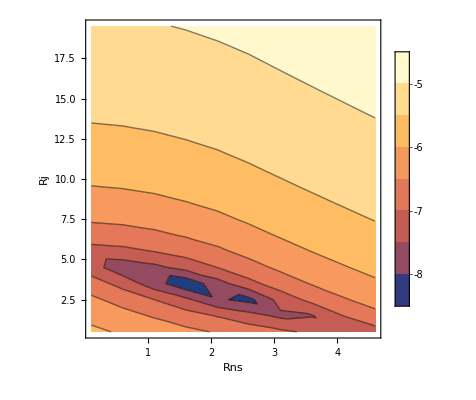

```mathematica
ListContourPlot[abc,PlotLegends->Automatic,FrameLabel->{{Rj,None},{Rns,None}}]
```

```mathematica
Show[%15,PlotLabel->None,LabelStyle->{15,GrayLevel[0]}]
```

-Graphics-

```mathematica
Export["~/"]
```